```mathematica
FunctE[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))+((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]
```

-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))+((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]

```mathematica
FunctE1[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))]
```

-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))]

```mathematica
FunctE2[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]
```

-Im[((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]

```mathematica
GammaSMLO[omega_,gammarx_,omegarx_]=gammarx*omega/omegarx
```

(gammarx omega)/omegarx

```mathematica
MainDirecroty=NotebookDirectory[]
```

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\

```mathematica
Filename="group_sn_50_120.dat";
DataExp=ReadList[FileNameJoin[{MainDirecroty,Filename}],Number];
Ncolumbs=3;
Nmaxpoints1=Length[DataExp]/Ncolumbs-1;
X1aver=Table[DataExp[[Ncolumbs*i+1]],{i,0,Nmaxpoints1}];
Y1aver=Table[DataExp[[Ncolumbs*i+2]],{i,0,Nmaxpoints1}];
dY1aver=Table[DataExp[[Ncolumbs*i+3]],{i,0,Nmaxpoints1}];
Clear[DataExp]
```

```mathematica
Needs["ErrorBarPlots`"]
```

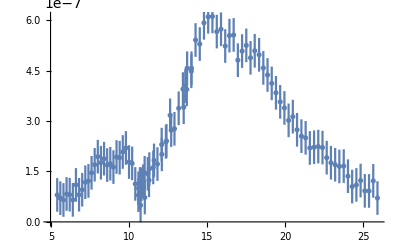

```mathematica
ErrorListPlot[{Transpose[{X1aver,Y1aver,dY1aver}]},PlotRange->All]
```

```mathematica
(* Fit  the cross section in the region [Ulow,Uupper] *)
```

```mathematica
Ulow=0.0;
Uupper=25.0;
Nlow=1;
Nupper=Length[Y1aver]
Do[If[X1aver[[i]]<Ulow,Nlow=i,Nlow=Nlow],{i,1,Length[Y1aver]}];
Do[If[X1aver[[i]]<Uupper,Nupper=i,Nupper=Nupper],{i,1,Length[Y1aver]}];
Nlow
Nupper
```

101

1

101

```mathematica
1
```

1

```mathematica
(*X1aver*)
```

```mathematica
(*Y1aver*)
```

```mathematica
(*dY1aver*)
```

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[(0.0000751051+((0.+«24» ⅈ) omega)/(66.7648+«1»«1»«1»))/(287.272+«1»«1»«1»+(3.01026×10^-12 «1»)/(66.7648+«1»-(«5»)^2))+(«1»)/(«1»)]]

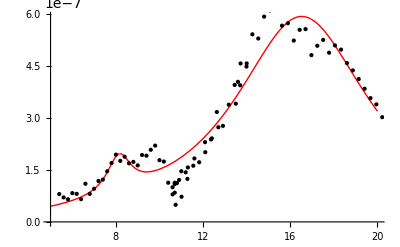

16.9491

8.17097

7.58102

1.36048

1.73501×10^-6

0.00866632

0.00109471

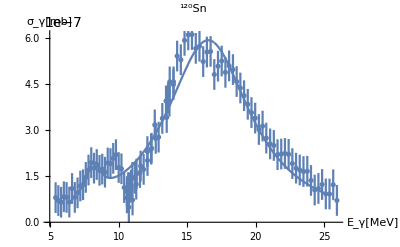

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 16.9491 | 0.103397 | 163.922 | 2.53991×10^-117
omega2p | 8.17097 | 0.307527 | 26.5699 | 1.71203×10^-45
Gamma1p | 7.58102 | 0.828681 | 9.14829 | 1.1898×10^-14
Gamma2p | 1.36048 | 0.87457 | 1.55559 | 0.123165
Gamma12p | 1.73501×10^-6 | 0.660772 | 2.62573×10^-6 | 0.999998
Z10 | 0.00866632 | 0.000130362 | 66.4789 | 7.83151×10^-81
Z20 | 0.00109471 | 0.000177909 | 6.15321 | 1.84485×10^-8

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{16.9491,0.103397,163.922,2.53991×10^-117},{8.17097,0.307527,26.5699,1.71203×10^-45},{7.58102,0.828681,9.14829,1.1898×10^-14},{1.36048,0.87457,1.55559,0.123165},{1.73501×10^-6,0.660772,2.62573×10^-6,0.999998},{0.00866632,0.000130362,66.4789,7.83151×10^-81},{0.00109471,0.000177909,6.15321,1.84485×10^-8}}

0.871202

0.871202

```mathematica
(*TSE  !!!!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,Nlow,Nmaxpointstemp}];
FordY1aver=Table[dY1aver[[i]],{i,Nlow,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,Nlow,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,Nlow,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,Gamma2p,Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0,13<omega1p < 20, 7<omega2p<10, 3<Gamma1p<8, 1<Gamma2p<3, 0<Gamma12p<6 (*, Z10<10, Z20<10*)
},{{omega1p,12},{omega2p,7},{Gamma1p,3},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEgam[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","120"],"Sn"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEgam=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[0.0000666629/(279.868+(0.+7.17985 ⅈ) omega-omega^2)+922196./(5.10761×10^9+«1»-omega^2)]]

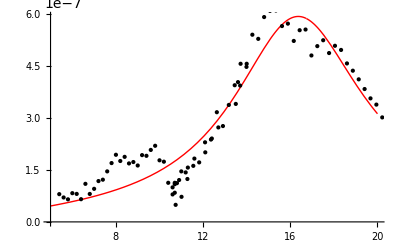

16.7293

71467.6

7.17985

55846.8

0.00816474

960.31

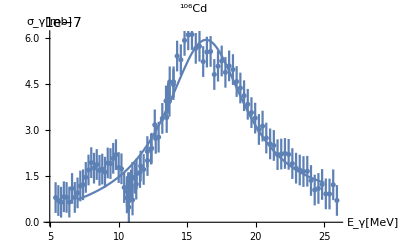

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-762.663] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 16.7293 | 0.133027 | 125.758 | 1.88636×10^-107
omega2p | 71467.6 | 5.99805 | 11915.1 | 4.21097×10^-295
Gamma1p | 7.17985 | 0.452108 | 15.8808 | 1.75383×10^-28
Gamma2p | 55846.8 | 1.91894 | 29103. | 0.
Z10 | 0.00816474 | 0.000316317 | 25.8119 | 1.02207×10^-44
Z20 | 960.31 | 223.191 | 4.30263 | 0.0000409662

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-762.663] is too small to represent as a normalized machine number; precision may be lost.

{{16.7293,0.133027,125.758,1.88636×10^-107},{71467.6,5.99805,11915.1,4.21097×10^-295},{7.17985,0.452108,15.8808,1.75383×10^-28},{55846.8,1.91894,29103.,0.},{0.00816474,0.000316317,25.8119,1.02207×10^-44},{960.31,223.191,4.30263,0.0000409662}}

1.04859

1.04859

```mathematica
(*independent Gamma12p=0 !!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,Gamma2p,0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0, 10<omega1p < 20 },{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEgam0[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEgam0=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FittedModel[-Im[(0.000378734+((0.+«18» ⅈ) omega)/(«1»))/(0.00103643+ⅈ («19»-«18» «5») omega-«1»+(17914.1 «1»)/(«1»))+(«17»+(«1»)/(«1»))/(«23»+«1»-«1»+(«1»)/(«1»))]]

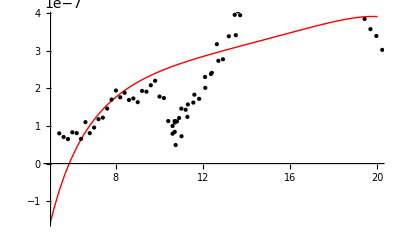

0.0321937

-0.0000280344

-0.169205

70246.3

133.844

0.0194611

231.752

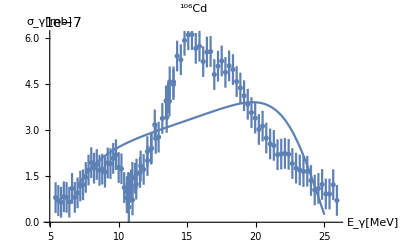

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 0.0321937 | 2816.17 | 0.0000114317 | 0.999991
omega2p | -0.0000280344 | 7.25971 | -3.86164×10^-6 | 0.999997
Gamma1p | -0.169205 | 14801.5 | -0.0000114316 | 0.999991
Gamma2p | 70246.3 | 340.712 | 206.175 | 1.17062×10^-126
Gamma12p | 133.844 | 134.474 | 0.995315 | 0.322138
Z10 | 0.0194611 | 0.0496505 | 0.391962 | 0.695974
Z20 | 231.752 | 3.00094×10^7 | 7.72262×10^-6 | 0.999994

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{0.0321937,2816.17,0.0000114317,0.999991},{-0.0000280344,7.25971,-3.86164×10^-6,0.999997},{-0.169205,14801.5,-0.0000114316,0.999991},{70246.3,340.712,206.175,1.17062×10^-126},{133.844,134.474,0.995315,0.322138},{0.0194611,0.0496505,0.391962,0.695974},{231.752,3.00094×10^7,7.72262×10^-6,0.999994}}

5.90651

5.90651

```mathematica
(*TSE SMLO GDR and PDR *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],GammaSMLO[omega,Gamma2p,omega2p],Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRsmloGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRsmloGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[(0.0000689226+((0.+«19» ⅈ) omega)/(«1»))/(280.009+«1»-«1»+(37.1823 («5»)^2)/(1.30776×10^8+«1»«1»«1»))+(«19»+(«1»)/(«1»))/(«21»+«1»«1»«1»+(«1»)/(«1»))]]

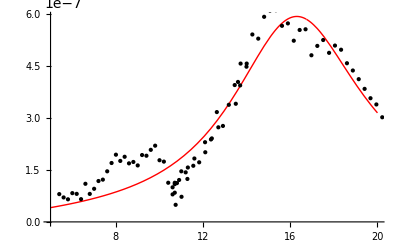

16.7335

11435.7

1.28994

8710.64

6.09773

0.00830196

56.8509

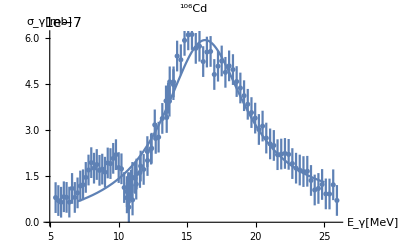

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 16.7335 | 3.68813 | 4.53712 | 0.0000168365
omega2p | 11435.7 | 2408.49 | 4.74809 | 7.33965×10^-6
Gamma1p | 1.28994 | 30.7213 | 0.0419886 | 0.966597
Gamma2p | 8710.64 | 1.7425×10^6 | 0.00499893 | 0.996022
Gamma12p | 6.09773 | 27.8919 | 0.21862 | 0.82742
Z10 | 0.00830196 | 0.00109835 | 7.55861 | 2.66366×10^-11
Z20 | 56.8509 | 5594.81 | 0.0101614 | 0.991914

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{16.7335,3.68813,4.53712,0.0000168365},{11435.7,2408.49,4.74809,7.33965×10^-6},{1.28994,30.7213,0.0419886,0.966597},{8710.64,1.7425×10^6,0.00499893,0.996022},{6.09773,27.8919,0.21862,0.82742},{0.00830196,0.00109835,7.55861,2.66366×10^-11},{56.8509,5594.81,0.0101614,0.991914}}

1.04968

1.04968

```mathematica
(*TSE SMLO GDR and PDG G=const !!!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],Gamma2p,Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,omega1p>0,omega2p>0,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRconsGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRconsGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FittedModel[-Im[(12112.3+((0.+«17» ⅈ) omega)/(291.634+«1»-(«5»)^2))/(«4»+(319853. «1»)/(291.634+«1»«1»«1»))+(«23»+(«1»)/(«1»))/(«18»+«1»-«1»+(«1»)/(«1»))]]

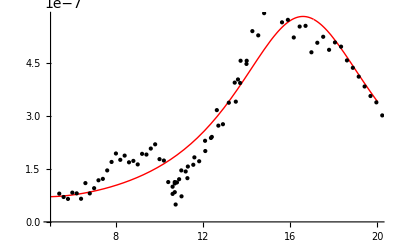

17.0773

6.90064×10^-8

-557.367

1259.61

565.555

0.00894224

110.056

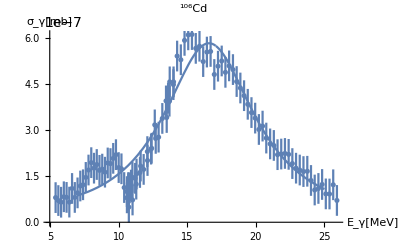

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 17.0773 | 0.231147 | 73.8808 | 4.61678×10^-85
omega2p | 6.90064×10^-8 | 0.000768119 | 0.0000898381 | 0.999929
Gamma1p | -557.367 | 62207.6 | -0.00895979 | 0.99287
Gamma2p | 1259.61 | 30.1823 | 41.7334 | 1.83663×10^-62
Gamma12p | 565.555 | 62207.5 | 0.00909143 | 0.992765
Z10 | 0.00894224 | 0.00113095 | 7.90686 | 5.00464×10^-12
Z20 | 110.056 | 612614. | 0.00017965 | 0.999857

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{17.0773,0.231147,73.8808,4.61678×10^-85},{6.90064×10^-8,0.000768119,0.0000898381,0.999929},{-557.367,62207.6,-0.00895979,0.99287},{1259.61,30.1823,41.7334,1.83663×10^-62},{565.555,62207.5,0.00909143,0.992765},{0.00894224,0.00113095,7.90686,5.00464×10^-12},{110.056,612614.,0.00017965,0.999857}}

1.08653

1.08653

```mathematica
(*TSE SMLO PDR and GDR G=const *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,GammaSMLO[omega,Gamma2p,omega2p],Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRsmloGDRcons[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRsmloGDRcons=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[0.0000757177/(291.111-(1.-0.473685 ⅈ) omega^2)+0.00442868/(28160.7-(1.-«18» ⅈ) («5»)^2)]]

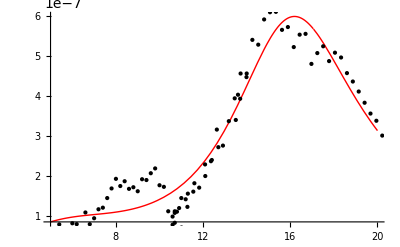

17.062

167.812

8.082

131639.

0.00870159

0.0665484

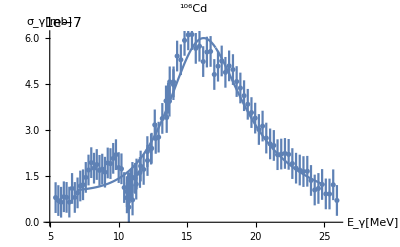

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 17.062 | 0.116489 | 146.468 | 1.0423×10^-113
omega2p | 167.812 | 159647. | 0.00105114 | 0.999164
Gamma1p | 8.082 | 0.650918 | 12.4163 | 1.32505×10^-21
Gamma2p | 131639. | 3.75811×10^8 | 0.000350281 | 0.999721
Z10 | 0.00870159 | 0.000438606 | 19.8392 | 1.49511×10^-35
Z20 | 0.0665484 | 63.3929 | 0.00104978 | 0.999165

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{17.062,0.116489,146.468,1.0423×10^-113},{167.812,159647.,0.00105114,0.999164},{8.082,0.650918,12.4163,1.32505×10^-21},{131639.,3.75811×10^8,0.000350281,0.999721},{0.00870159,0.000438606,19.8392,1.49511×10^-35},{0.0665484,63.3929,0.00104978,0.999165}}

0.807296

0.807296

```mathematica
(*independent Gamma12p=0, SMLO GDR and PDG *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],GammaSMLO[omega,Gamma2p,omega2p],0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRsmloGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRsmloGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[0.0830421/(348549.+(0.+149950. ⅈ) omega-omega^2)+0.0000718701/(288.456-(1.-«20» ⅈ) «1»)]]

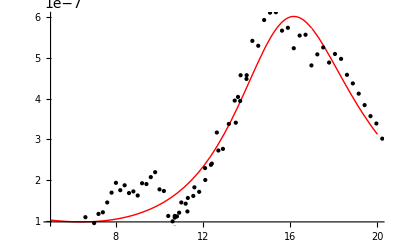

16.984

590.38

7.83989

149950.

0.00847762

0.28817

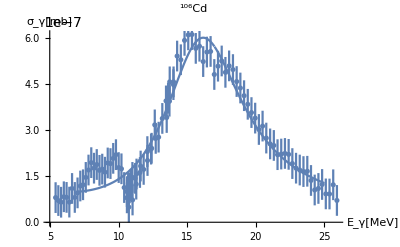

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-891.206] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 16.984 | 0.119894 | 141.659 | 2.45027×10^-112
omega2p | 590.38 | 676.414 | 0.872809 | 0.384968
Gamma1p | 7.83989 | 0.571507 | 13.7179 | 2.93255×10^-24
Gamma2p | 149950. | 1.3316 | 112609. | 0.
Z10 | 0.00847762 | 0.00033763 | 25.1092 | 1.0095×10^-43
Z20 | 0.28817 | 0.0750945 | 3.83743 | 0.000223872

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-891.206] is too small to represent as a normalized machine number; precision may be lost.

{{16.984,0.119894,141.659,2.45027×10^-112},{590.38,676.414,0.872809,0.384968},{7.83989,0.571507,13.7179,2.93255×10^-24},{149950.,1.3316,112609.,0.},{0.00847762,0.00033763,25.1092,1.0095×10^-43},{0.28817,0.0750945,3.83743,0.000223872}}

0.837299

0.837299

```mathematica
(*independent Gamma12p=0, SMLO GDR and PDG G=const !!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],Gamma2p,0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRconsGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRconsGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[0.0000502339/(252.577+(0.+6.22838 ⅈ) omega-omega^2)+0.0000259779/(398.655-(1.-«1») «1»)]]

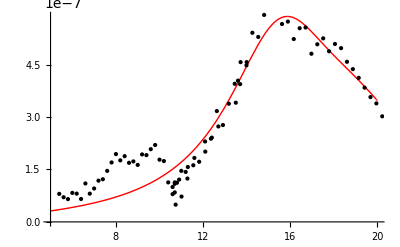

15.8927

19.9664

6.22838

7.25412

0.00708759

0.00509685

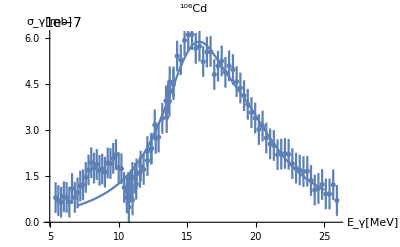

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 15.8927 | 0.32577 | 48.785 | 4.6506×10^-69
omega2p | 19.9664 | 0.745882 | 26.7688 | 4.86762×10^-46
Gamma1p | 6.22838 | 0.437611 | 14.2327 | 2.75286×10^-25
Gamma2p | 7.25412 | 2.01286 | 3.60389 | 0.000501409
Z10 | 0.00708759 | 0.000678775 | 10.4417 | 1.88629×10^-17
Z20 | 0.00509685 | 0.00120175 | 4.24118 | 0.0000516138

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{15.8927,0.32577,48.785,4.6506×10^-69},{19.9664,0.745882,26.7688,4.86762×10^-46},{6.22838,0.437611,14.2327,2.75286×10^-25},{7.25412,2.01286,3.60389,0.000501409},{0.00708759,0.000678775,10.4417,1.88629×10^-17},{0.00509685,0.00120175,4.24118,0.0000516138}}

0.969712

0.969712

```mathematica
(*independent Gamma12p=0, SMLO PDR and GDR G=const *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,GammaSMLO[omega,Gamma2p,omega2p],0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRsmloGDRcons[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRsmloGDRcons=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

```mathematica
"E:\\Sasha\\work\\Students\\Kucher\\Cd106\\FigSigmaFit106Cd.eps"
```

E:\Sasha\work\Students\Kucher\Cd106\FigSigmaFit106Cd.eps

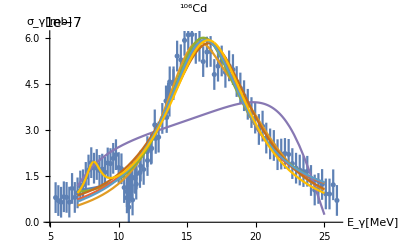

```mathematica
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[{ResponseFuncPDRsmloGDRsmlo[x],ResponseFuncPDRsmloGDRcons[x],ResponseFuncPDRconsGDRsmlo[x],ResponseFuncTSEgam0[x],ResponseFuncTSEPDRsmloGDRsmlo[x],ResponseFuncTSEPDRsmloGDRcons[x],ResponseFuncTSEPDRconsGDRsmlo[x],ResponseFuncTSEgam[x]},{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
```

```mathematica
Chi2PDRsmloGDRsmlo
Chi2PDRsmloGDRcons
Chi2PDRconsGDRsmlo
Chi2TSEgam0
Chi2TSEPDRsmloGDRsmlo
Chi2TSEPDRsmloGDRcons
Chi2TSEPDRconsGDRsmlo
Chi2TSEgam
```

0.807296

0.969712

0.837299

1.04859

5.90651

1.08653

1.04968

0.871202